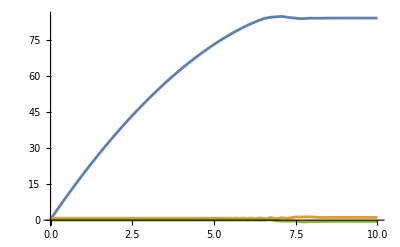

```mathematica
i=0.000103624;
w=20;
d=0.13;
x1=d;
y1=0;
x2=2*d;
y2=0;
r=0.057;
tmax=10;
number=4;
first=Table[th1[t]+i*2*Pi/number,{i,0,number-1}];
second=Table[th2[t]+i*2*Pi/number,{i,0,number-1}];
third=Table[th3[t]+i*2*Pi/number,{i,0,number-1}];
connectingVector[th1_,th2_,posx1_,posx2_,posy1_,posy2_]:={posx2+r*Cos[th2]-posx1-r*Cos[th1],posy2+r*Sin[th2]-posy1-r*Sin[th1],0};
distance[th1_,th2_,posx1_,posx2_,posy1_,posy2_]:=Norm[connectingVector[th1,th2,posx1,posx2,posy1,posy2]];
forceMagnitude[l_]:=Exp[-17.722]/l^4.6371;
forceVector[th1_,th2_,posx1_,posx2_,posy1_,posy2_]:=forceMagnitude[distance[th1,th2,posx1,posx2,posy1,posy2]]*connectingVector[th1,th2,posx1,posx2,posy1,posy2]/distance[th1,th2,posx1,posx2,posy1,posy2];
torque[th1_,th2_,posx1_,posx2_,posy1_,posy2_]:=Cross[{r*Cos[th1],r*Sin[th1],0},-forceVector[th1,th2,posx1,posx2,posy1,posy2]][[3]];
M1=Sum[torque[first[[n]],second[[k]],0,x1,0,y1],{n,1,number},{k,1,number}]+Sum[torque[first[[n]],third[[k]],0,x2,0,y2],{n,1,number},{k,1,number}];
M2=Sum[torque[second[[n]],first[[k]],x1,0,y1,0],{n,1,number},{k,1,number}]+Sum[torque[second[[n]],third[[k]],x1,x2,y1,y2],{n,1,number},{k,1,number}];
M3=Sum[torque[third[[n]],first[[k]],x2,0,y2,0],{n,1,number},{k,1,number}]+Sum[torque[third[[n]],second[[k]],x2,x1,y2,y1],{n,1,number},{k,1,number}];
sol=NDSolve[{th1''[t]==M1/i-2.1 * Sign[th1'[t]],th2''[t]==M2/i-4 * Sign[th2'[t]],th3''[t]==M3/i-3.2 * Sign[th3'[t]],th1[0]==0.3,th1'[0]==w,th2[0]==Pi/4,th2'[0]==0,th3[0]==0,th3'[0]==0},{th1,th2,th3},{t,0,tmax},PrecisionGoal->10,AccuracyGoal->10];
Plot[{th1[t]/.sol,th2[t]/.sol,th3[t]/.sol},{t,0,tmax},PlotRange->All]
Animate[Show[Join[Table[Graphics[Point[{r*Cos[first[[i]]],r*Sin[first[[i]]]}]],{i,1,number}]/.sol[[1]],Table[Graphics[Point[{x1+r*Cos[second[[i]]],y1+r*Sin[second[[i]]]}]],{i,1,number}]/.sol[[1]],
Table[Graphics[Point[{x2+r*Cos[third[[i]]],y2+r*Sin[third[[i]]]}]],{i,1,number}]/.sol[[1]]],PlotRange->{{-1.1*r,5.9*r},{-1.1*r,1.1*r}}]/.{t->k},{k,0,tmax},AnimationRate->0.1]
```

```mathematica
sol
```

{{th→th,th0→th0}}